# Using the GLO package - example

# Overview Fix an even number of modes n. Initialize a product state of squeezed states. Send these through layers of random passive linear optical transformations. Each layer is a one-dimensional “brickwork” structure. Below is an example of n=6 and two layers of the brickwork. Each gate/rectangle is a random two-mode passive transformation. Notice that a layer encompasses two columns; the first column I call the “odd” transformations, and the second the “even”. -Graphics- After each layer, we calculate the purity of the reduced density matrix describing the state of the first n/2 modes; the purity is simply 1/Sqrt[Det[covariance matrix of the first n/2 modes]], and the Renyi-2 entropy is -Log[purity]. Note that the von-Nuemann/entanglement entropy is always ≥ the Renyi-2 entropy. This is one simulation; preparing a product state and simulating a certain number of layers and computing the purity after each layer. We do many simulations, and then average the results so that we are left with the average purity/Renyi-2 entropy as a function of depth. We do this for many n, and plot the result.

### Clear all variables

```mathematica
Remove["GLO`*"];
Remove["Global`*"];
```

### Import GLO package

```mathematica
Get["~/Documents/Wolfram Mathematica/GLO/functions/GLO.wl"];
```

## Simulation details

### Choose various numbers of modes to simulate (all must be even!)

```mathematica
ns={20,30};
nsLabels=Table["num modes: " <> ToString[n],{n,ns}];
```

### Squeezing parameter for each mode For now, we set all of the squeezing parameters to 1/√n.

```mathematica
squeeze[n_]:=N@Table[1/(√n),n];
```

### Choose a depth to simulate to

```mathematica
maxdepth=200;
```

### Choose how many simulations to run in order to estimate the average

```mathematica
iters=20;
```

### Choose which quantities to calculate You can define your own quantities or use some predefined ones. Each quantity should be a function of the covariance matrix. Here I will choose the quantities to be the purity, Renyi-2 entropy, and entanglement entropy of the first n/2 modes. Thus we partition the system around mode n/2. The function purityOfPartition[v,m] computes the purity of modes 1 through m of the covariance matrix v. Thus, we want to compute the function purityOfPartition[#,n/2]&. And this is similar for the Renyi-2 entropy, entanglement entropy, and logorithmic negativity.

```mathematica
quantities[n_]:={
purityOfLeftPartition[#,n/2]&,
renyi2EntropyOfLeftPartition[#,n/2]&,
entanglementEntropyOfLeftPartition[#,n/2]&
(*logNegativityOfLeftPartition[#,n/2]&*)
};
quantityLabels={"purity","Renyi-2 entropy","entanglement entropy"};
```

## 1D brickwork structure: random Now we will simulate with layers of random brickwork for each n∈ns. The last argument of simulate is the layer function. It should be a function of no parameters. In this case, oneDimRandomBrickworkLayer is a function of one parameter: the number of modes. We make it a function of zero parameters by oneDimRandomBrickworkLayer[n]&.

```mathematica
randBrick=Table[
simulate[
squeeze[n],maxdepth,iters,quantities[n],
oneDimRandomBrickworkLayer[n]&
],
{n,ns}];
```

### Plot results

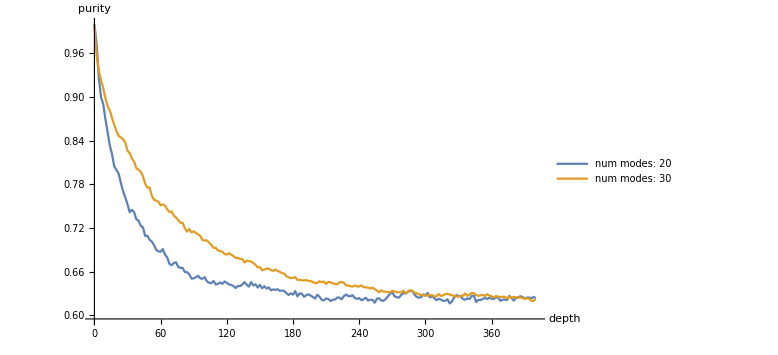
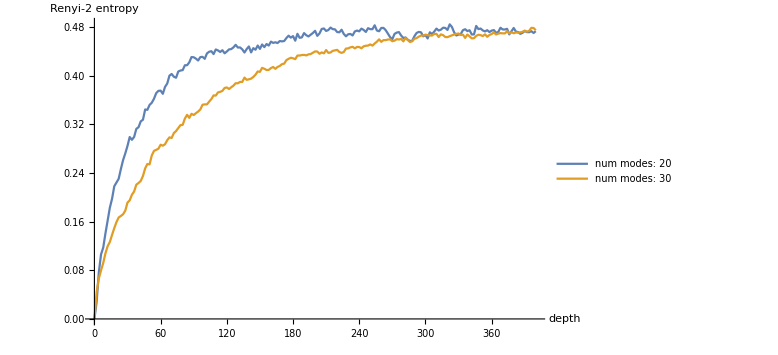
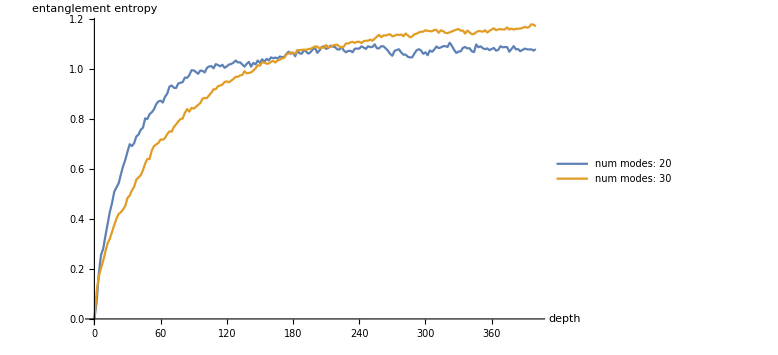

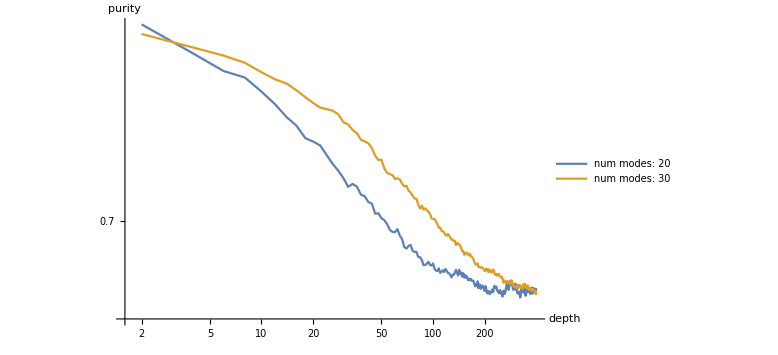
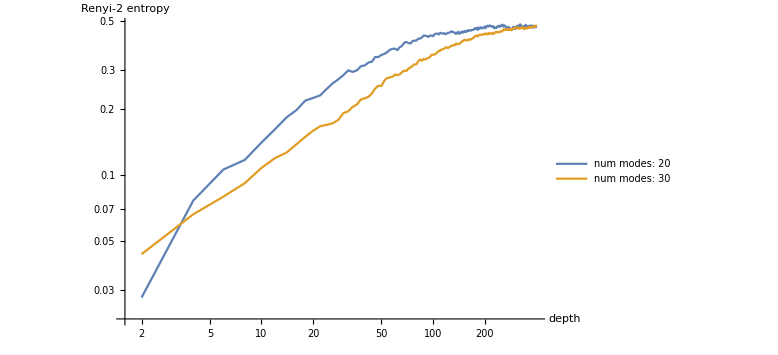
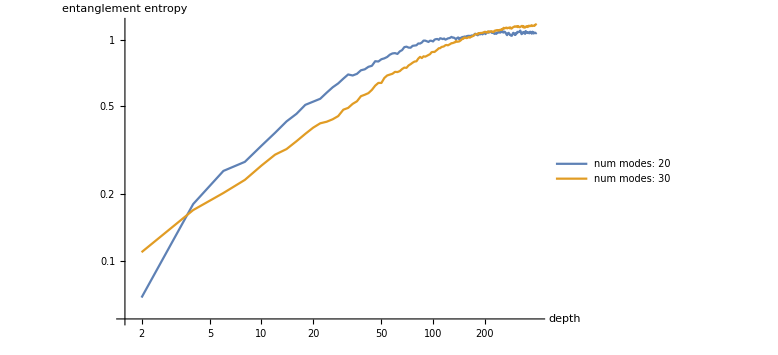

```mathematica
plotLinearLinearQuantities[randBrick,quantityLabels,nsLabels]
(*plotLinearLogQuantities[randBrick,quantityLabels,nsLabels]*)
(*plotLogLinearQuantities[randBrick,quantityLabels,nsLabels]*)
plotLogLogQuantities[randBrick,quantityLabels,nsLabels]
```

## 1D brickwork structure: ACTIVE random Now we will simulate with layers of random brickwork for each n∈ns. The last argument of simulate is the layer function. It should be a function of no parameters. In this case, oneDimRandomActiveBrickworkLayer is a function of three parameters: the number of modes and the min and max squeezing values.. We make it a function of zero parameters by oneDimRandomActiveBrickworkLayer[n,rmin,rmax]&. Since we’re introducing active componenents, we will set the initial squeezing to zero.

```mathematica
randActiveBrick=Table[
simulate[
Table[0,n],maxdepth,iters,quantities[n],
oneDimRandomActiveBrickworkLayer[n,-1/(√n),1/(√n)]&
],
{n,ns}];
```

### Plot results

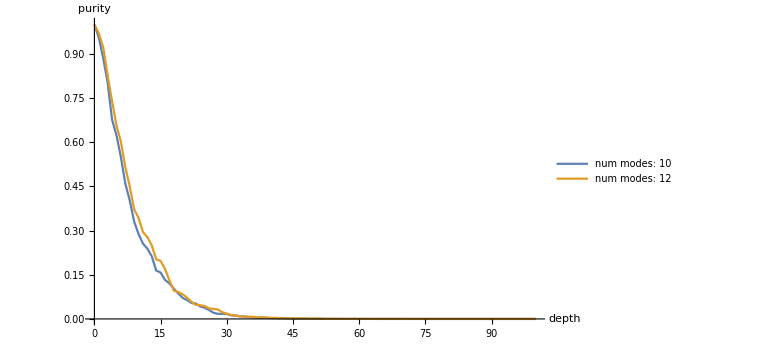
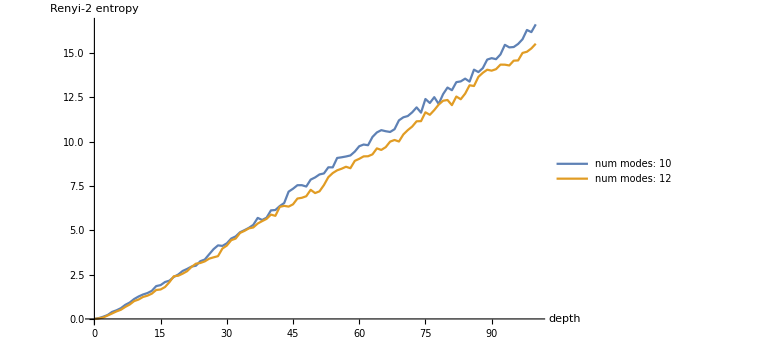
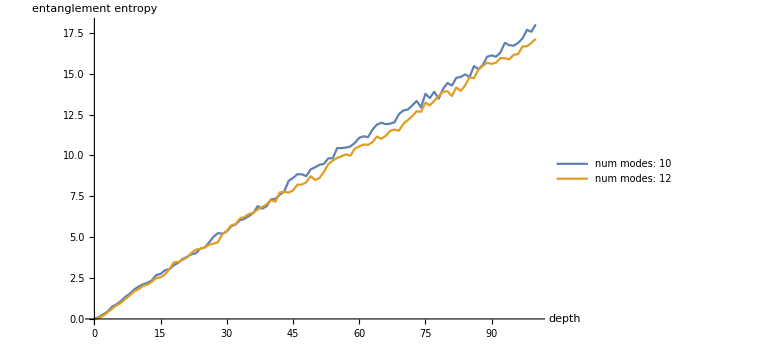

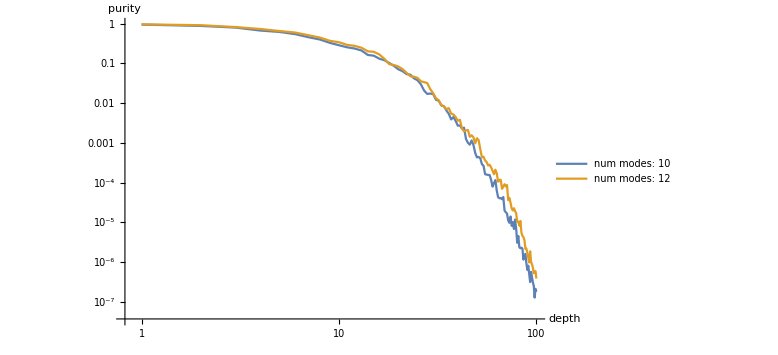
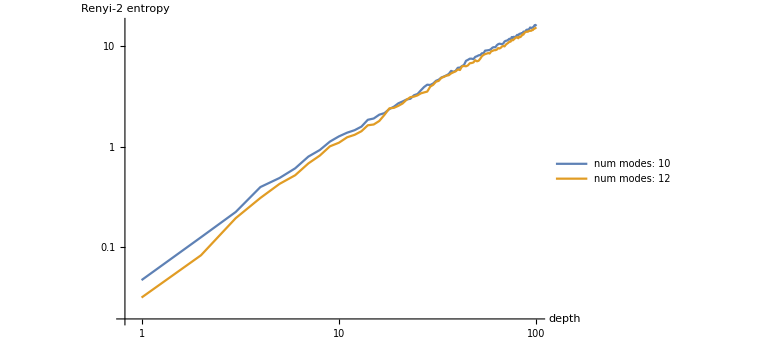
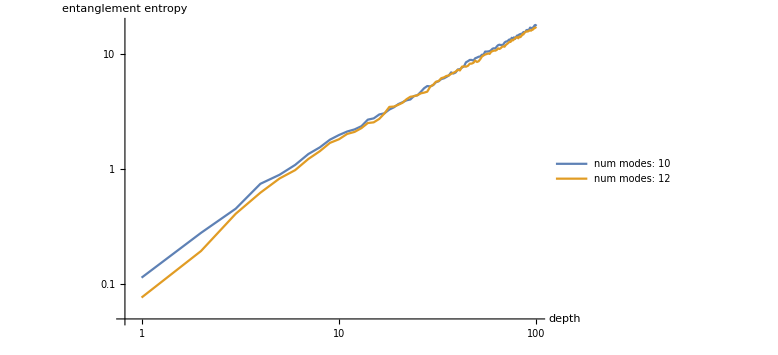

```mathematica
plotLinearLinearQuantities[randActiveBrick,quantityLabels,nsLabels]
(*plotLinearLogQuantities[randActiveBrick,quantityLabels,nsLabels]*)
(*plotLogLinearQuantities[randActiveBrick,quantityLabels,nsLabels]*)
plotLogLogQuantities[randActiveBrick,quantityLabels,nsLabels]
```

## 1D brickwork structure: fixed beamsplitter, random phases Now we will simulate for each n∈ns with layers of brickwork with one fixed global beamsplitter while phases are still random. The last argument of simulate is the layer function. It should be a function of no parameters. In this case, oneDimFixedBeamsplitterBrickworkLayer is a function of two parameters: the number of modes and the beamsplitter angle. We make it a function of zero parameters by oneDimFixedBeamsplitterBrickworkLayer[n,θ]&.

```mathematica
θ=RandomReal[2Pi];
fixedBeamBrick=Table[
simulate[
squeeze[n],maxdepth,iters,quantities[n],
oneDimFixedBeamsplitterBrickworkLayer[n,θ]&
],
{n,ns}];
```

### Plot results

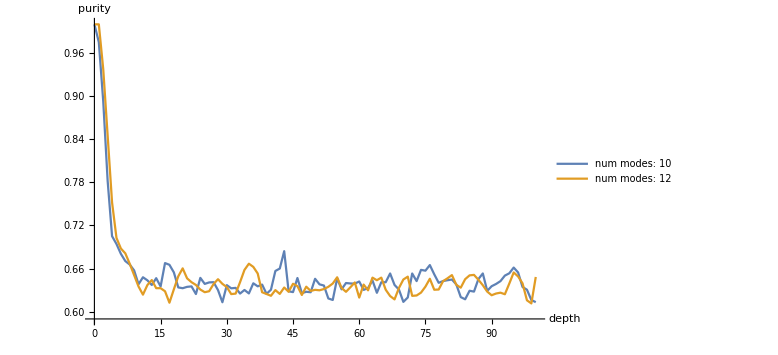
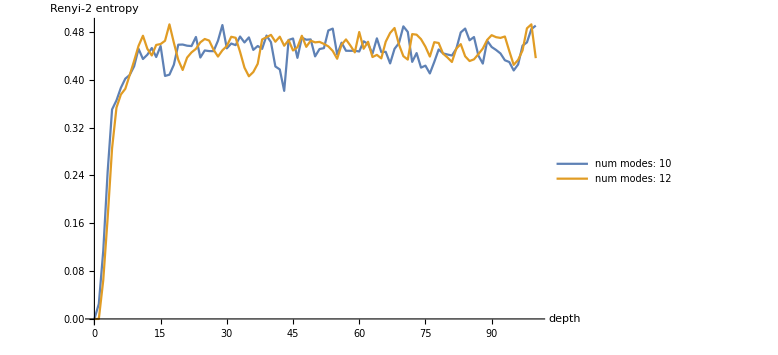
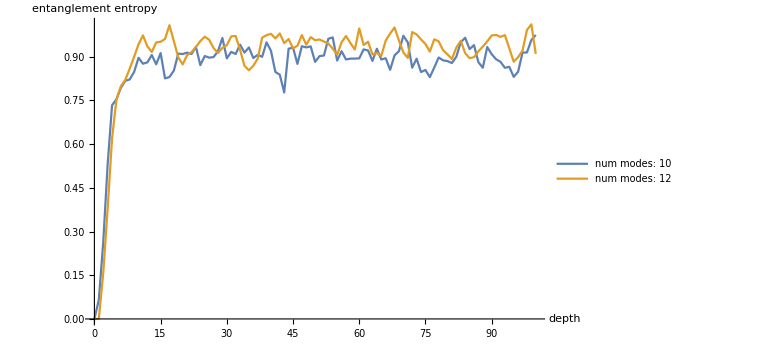

```mathematica
plotLinearLinearQuantities[fixedBeamBrick,quantityLabels,nsLabels]
(*plotLinearLogQuantities[fixedBeamBrick,quantityLabels,nsLabels]*)
(*plotLogLinearQuantities[fixedBeamBrick,quantityLabels,nsLabels]*)
(*plotLogLogQuantities[fixedBeamBrick,quantityLabels,nsLabels]*)
```

## 1D brickwork structure: fixed beamsplitter and phases Now we will simulate for each n∈ns with layers of brickwork with one fixed global beamsplitter and one fixed global phase. The last argument of simulate is the layer function. It should be a function of no parameters. In this case, oneDimFixedBrickworkLayer is a function of three parameters: the number of modes, the beamsplitter angle, and the phaseshifter angle. We make it a function of zero parameters by oneDimFixedBrickworkLayer[n,θ,ϕ]&.

```mathematica
(*use same θ beamsplitter angle from above*)
ϕ=RandomReal[2Pi];
fixedBrick=Table[
simulate[
squeeze[n],maxdepth,iters,quantities[n],
oneDimFixedBrickworkLayer[n,θ,ϕ]&
],
{n,ns}];
```

### Plot results

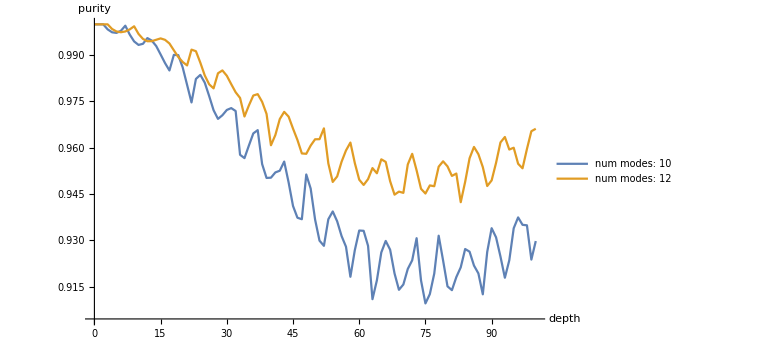
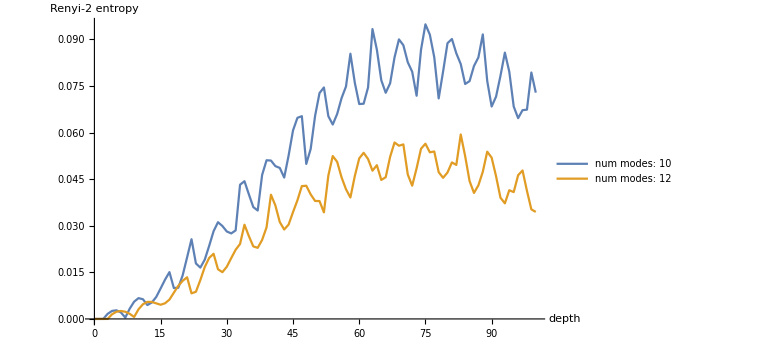
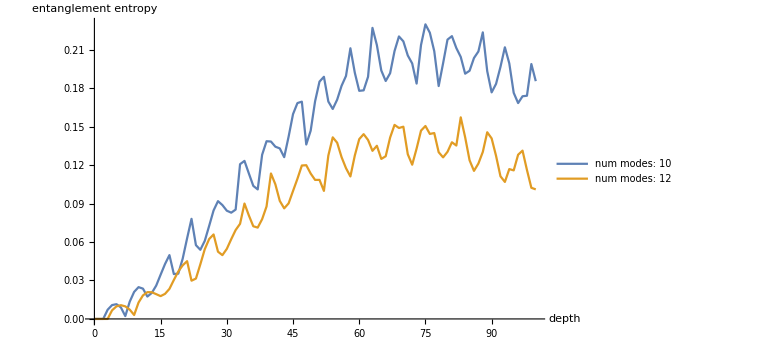

```mathematica
plotLinearLinearQuantities[fixedBrick,quantityLabels,nsLabels]
(*plotLinearLogQuantities[fixedBrick,quantityLabels,nsLabels]*)
(*plotLogLinearQuantities[fixedBrick,quantityLabels,nsLabels]*)
(*plotLogLogQuantities[fixedBrick,quantityLabels,nsLabels]*)
```

# Add in measurements

### "Monitored random circuit"; measure at a rate p

```mathematica
p=.01;
```

## 1D brickwork structure: random Now we will simulate with layers of random brickwork for each n∈ns. The last argument of simulate is the layer function. It should be a function of no parameters. In this case, oneDimRandomBrickworkLayer is a function of one parameter: the number of modes. We make it a function of zero parameters by oneDimRandomBrickworkLayer[n]&.

```mathematica
randBrickMeasurements=Table[
simulateWithMeasurements[
p,squeeze[n],maxdepth,iters,quantities[n],
oneDimRandomBrickworkLayer[n]&
],
{n,ns}];
```

### Plot results

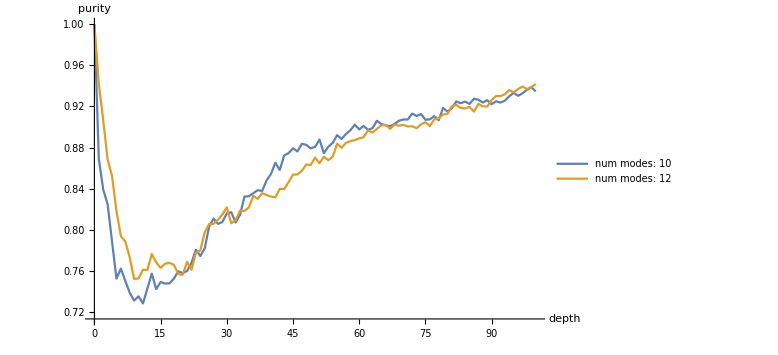
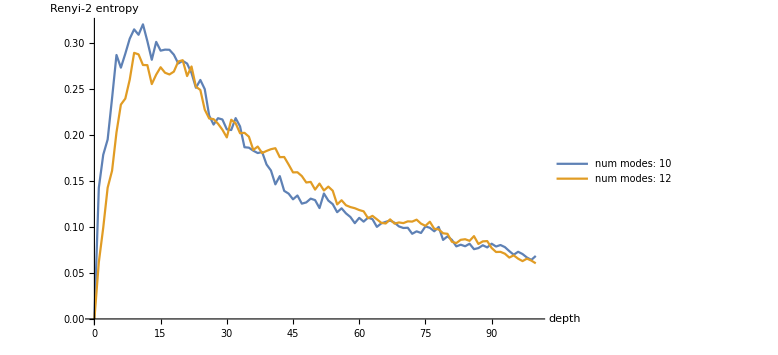
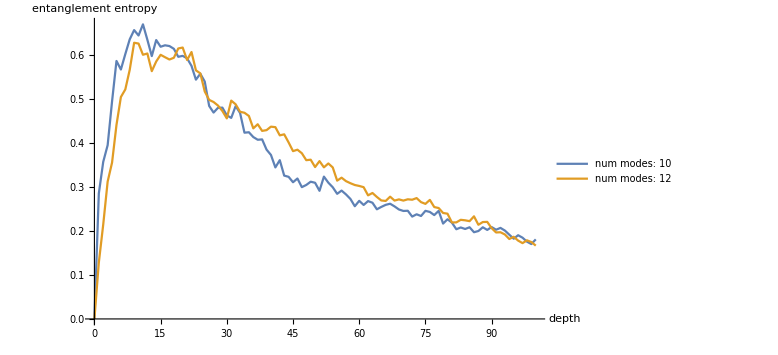

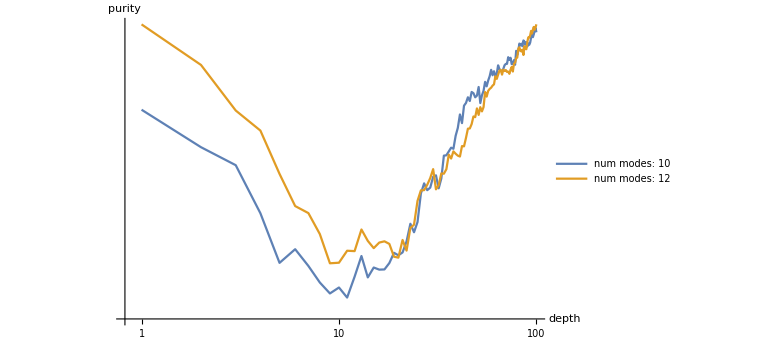
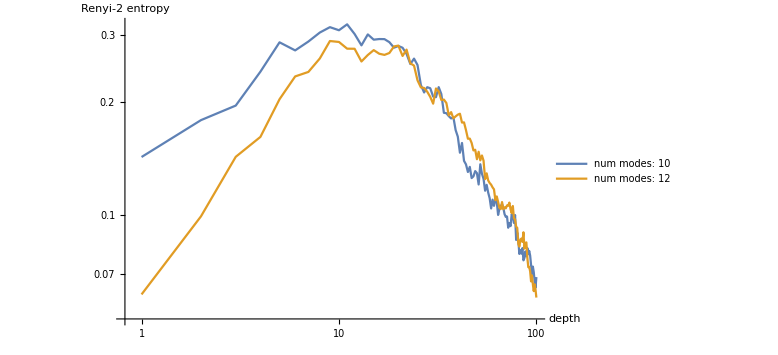
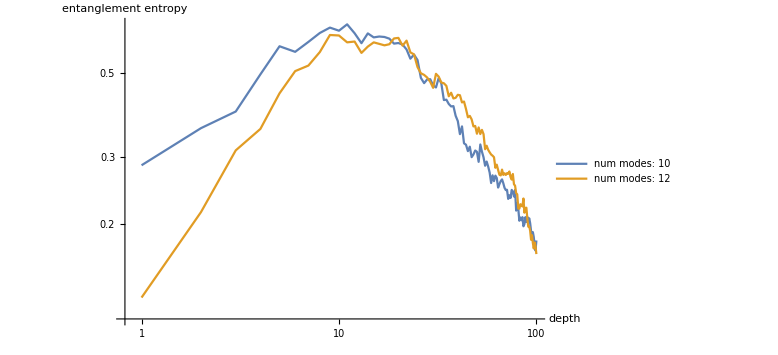

```mathematica
plotLinearLinearQuantities[randBrickMeasurements,quantityLabels,nsLabels]
(*plotLinearLogQuantities[randBrickMeasurements,quantityLabels,nsLabels]*)
(*plotLogLinearQuantities[randBrickMeasurements,quantityLabels,nsLabels]*)
plotLogLogQuantities[randBrickMeasurements,quantityLabels,nsLabels]
```

## 1D brickwork structure: ACTIVE random Now we will simulate with layers of random brickwork for each n∈ns. The last argument of simulate is the layer function. It should be a function of no parameters. In this case, oneDimRandomActiveBrickworkLayer is a function of three parameters: the number of modes and the min and max squeezing values.. We make it a function of zero parameters by oneDimRandomActiveBrickworkLayer[n,rmin,rmax]&. Since we’re introducing active componenents, we will set the initial squeezing to zero.

```mathematica
randActiveBrickMeasurements=Table[
simulateWithMeasurements[
p,Table[0,n],maxdepth,iters,quantities[n],
oneDimRandomActiveBrickworkLayer[n,-1/(√n),1/(√n)]&
],
{n,ns}];
```

### Plot results

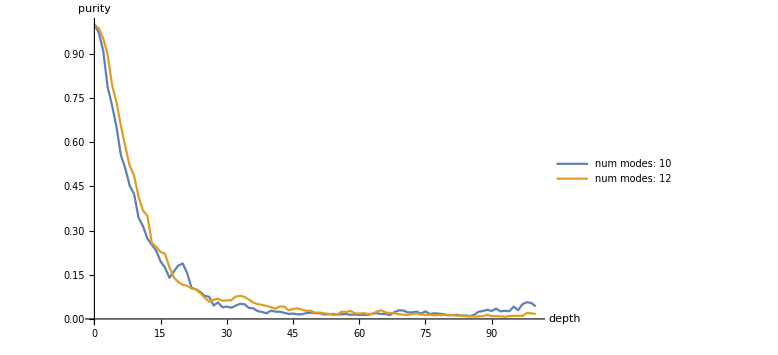
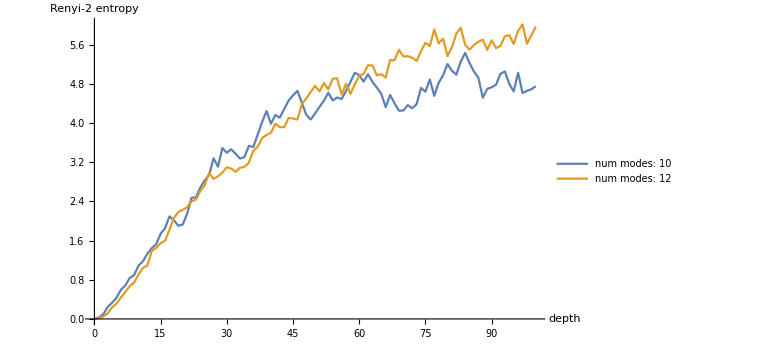
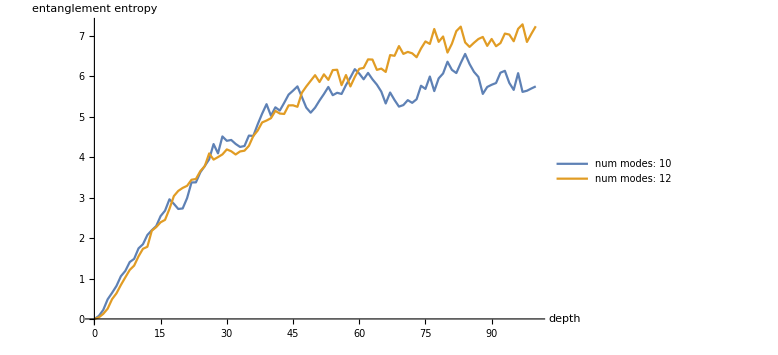

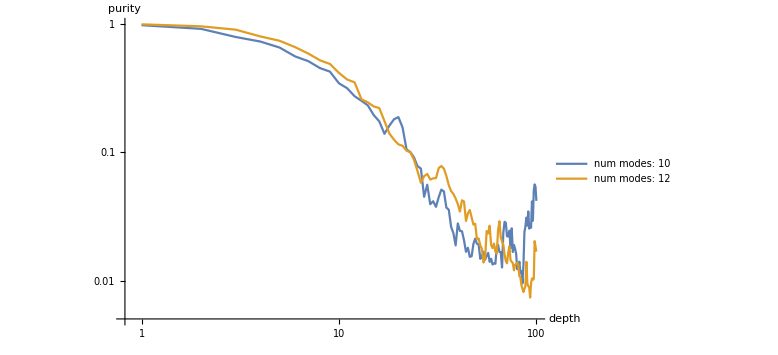
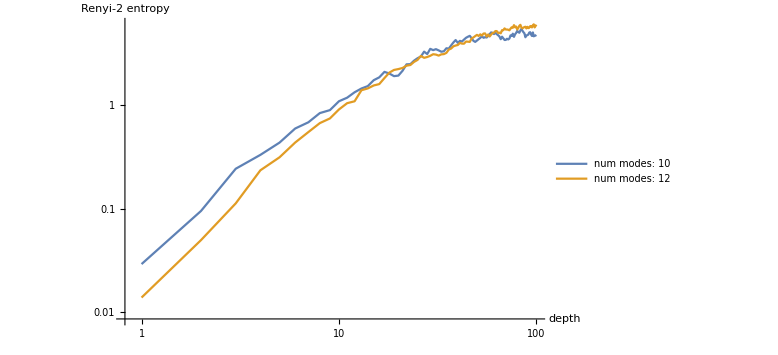
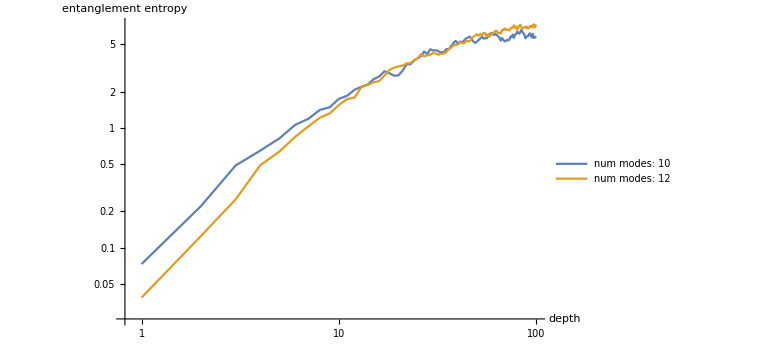

```mathematica
plotLinearLinearQuantities[randActiveBrickMeasurements,quantityLabels,nsLabels]
(*plotLinearLogQuantities[randActiveBrickMeasurements,quantityLabels,nsLabels]*)
(*plotLogLinearQuantities[randActiveBrickMeasurements,quantityLabels,nsLabels]*)
plotLogLogQuantities[randActiveBrickMeasurements,quantityLabels,nsLabels]
```